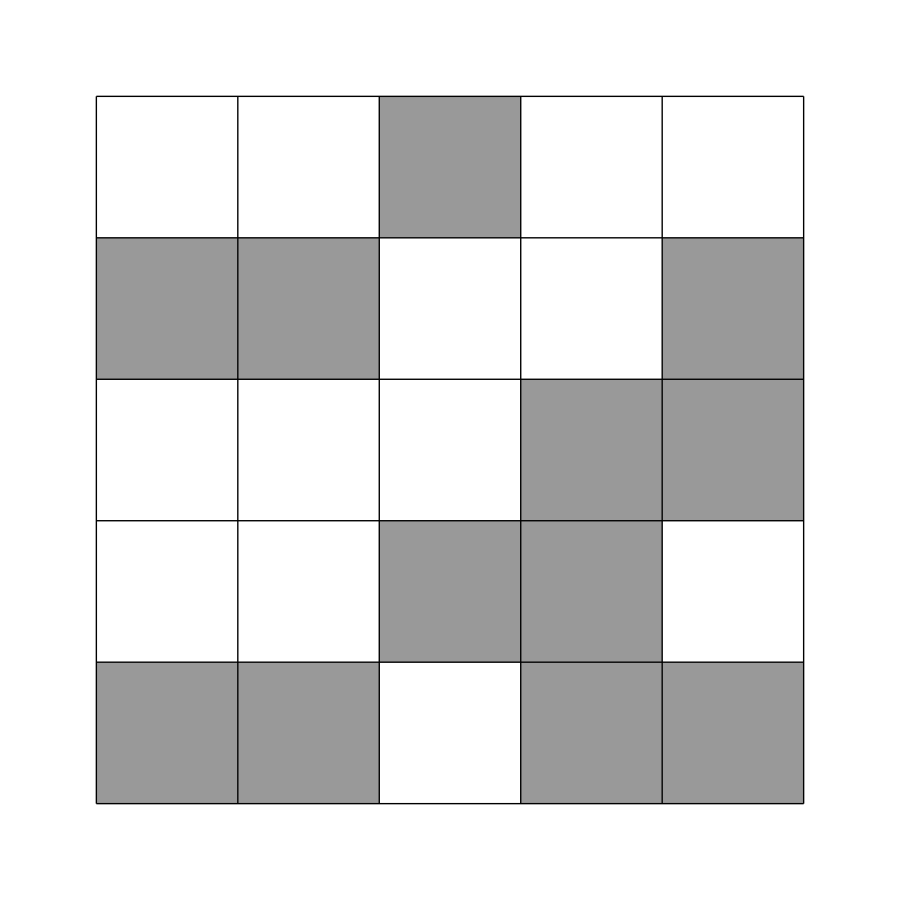

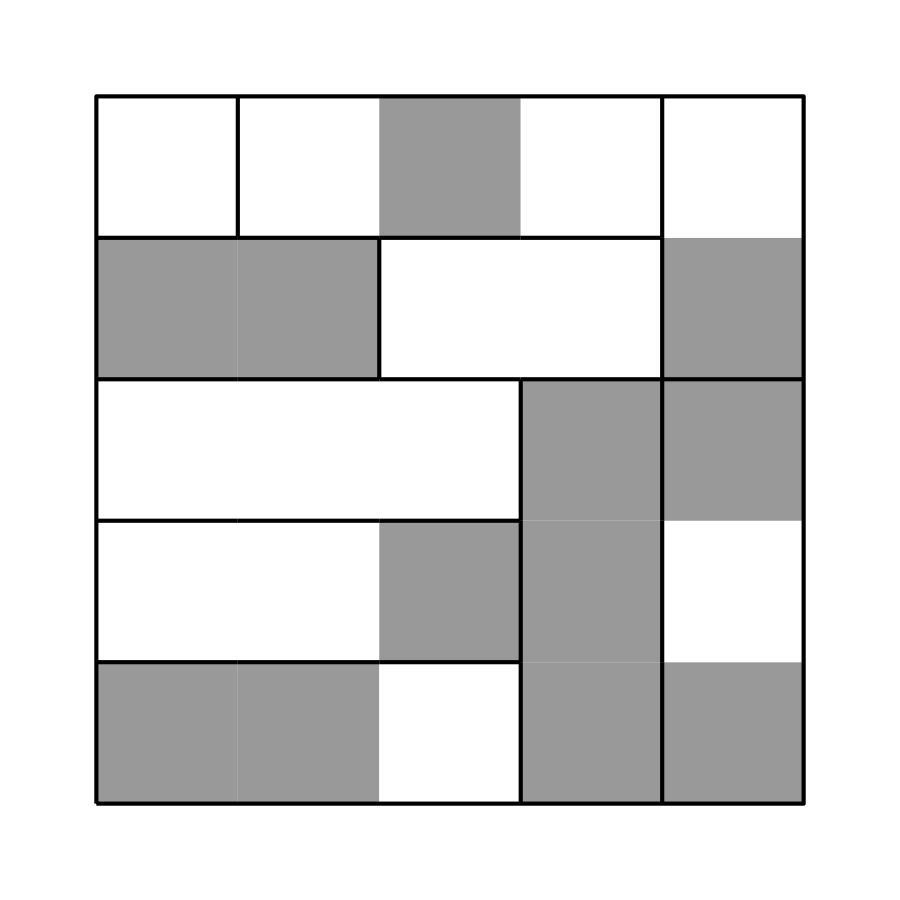

```mathematica
A={{}};
B=Flatten[Table[{i,j},{i,5},{j,5}],1];
While[Length[A[[1]]]<10,
top=First[A];
A=Rest[A];
new=Complement[B,Flatten[top,1]][[1]];
poss=Select[{{new},{new,new+{1,0}},{new,new+{1,0},new+{2,0}},{new,new+{0,1}},{new,new+{0,1},new+{0,2}}},Intersection[#,Flatten[top,1]]=={}&&Complement[#,B]=={}&];
If[Length[Select[top,Length[#]==3&]]==6,
poss=Select[poss,Length[#]=!=3&]];
If[Length[Select[top,Length[#]==2&]]==3,
poss=Select[poss,Length[#]=!=2&]];
If[Length[Select[top,Length[#]==1&]]==1,
poss=Select[poss,Length[#]=!=1&]];
A=A~Join~Map[Append[top,#]&,poss]];
```

```mathematica
Length[A]
```

3664

```mathematica
strip[L_]:=Map[M[[Apply[Sequence,#]]]&,L]
```

```mathematica
strips[L_]:=(Rest[Rest[Sort[Map[strip,L]~Join~Map[Reverse[strip[#]]&,L]]]]=={{1,1},{1,1},{1,2},{2,1},{2,2},{2,2},{1,1,1},{1,1,1},{1,1,2},{1,2,1},{1,2,1},{1,2,2},{2,1,1},{2,1,2},{2,1,2},{2,2,1},{2,2,2},{2,2,2}})
```

```mathematica
pic[M_]:=Style[Show[Graphics[{MapIndexed[{GrayLevel[0.4 (#1-1)+0.6],Rectangle[#2,#2+{1,1}]}&,M,{2}],GrayLevel[0],Table[Line[{{1,i},{6,i}}],{i,1,6}],Table[Line[{{i,1},{i,6}}],{i,1,6}]}],AspectRatio->Automatic,PlotRange->{{0.9,6.1},{0.9,6.1}},ImageSize->120],Antialiasing->False]
```

```mathematica
sol[L_,M_]:=Style[Show[Graphics[{MapIndexed[{GrayLevel[0.4 (#1-1)+0.6],Rectangle[#2,#2+{1,1}]}&,M,{2}],GrayLevel[0],AbsoluteThickness[3],Table[If[Position[L,{i,j}]⟦1,1⟧=!=Position[L,{i+1,j}]⟦1,1⟧,Line[{{i+1,j},{i+1,j+1}}],{}],{i,1,4},{j,1,5}],Table[If[Position[L,{i,j}]⟦1,1⟧=!=Position[L,{i,j+1}]⟦1,1⟧,Line[{{i+1,j+1},{i,j+1}}],{}],{i,1,5},{j,1,4}],Line[{{1,1},{6,1},{6,6},{1,6},{1,1}}]}],AspectRatio->Automatic,PlotRange->{{0.9,6.1},{0.9,6.1}},ImageSize->120],Antialiasing->False]
```

```mathematica
For[k=1,k≤1000000,k++,
M=Table[Random[Integer,{1,2}],{5},{5}];
While[Not[11<Count[M,1,Infinity]<14],M=Table[Random[Integer,{1,2}],{5},{5}]];
u=Select[A,strips];
If[Length[u]==1,Print[pic[M]];Print[sol[u[[1]],M]]]
]
```

$Aborted

## 5x5

-Graphics-

-Graphics-

-Graphics-

«213 more identical outputs»

## 6x9 code

```mathematica
A={{}};
B=Flatten[Table[{i,j},{i,6},{j,9}],1];
While[Length[A[[1]]]<15,
If[Length[A]>1,If[Length[A[[1]]]<Length[A[[2]]],Print["length=",Length[A[[2]]],"  number=",Length[A]]]];
top=First[A];
A=Rest[A];
new=Complement[B,Flatten[top,1]][[1]];
poss=Select[{{new,new+{1,0},new+{2,0}},{new,new+{1,0},new+{2,0},new+{3,0}},{new,new+{0,1},new+{0,2}},{new,new+{0,1},new+{0,2},new+{0,3}}},Intersection[#,Flatten[top,1]]=={}&&Complement[#,B]=={}&];
If[Length[Select[top,Length[#]==3&]]==6,
poss=Select[poss,Length[#]=!=3&]];
If[Length[Select[top,Length[#]==4&]]==9,
poss=Select[poss,Length[#]=!=4&]];
A=A~Join~Map[Append[top,#]&,poss]];
```

length=2  number=13

length=3  number=56

length=4  number=177

length=5  number=553

length=6  number=1650

length=7  number=4742

length=8  number=12828

length=9  number=32565

length=10  number=68475

length=11  number=108176

length=12  number=117273

length=13  number=64345

length=14  number=15127

length=15  number=5580

```mathematica
Length[A]
```

5580

```mathematica
cannon[L_]:=Sort[{L,Reverse[L]}][[1]]
```

```mathematica
strip[L_]:=Map[M[[Apply[Sequence,#]]]&,L]
```

```mathematica
strips[L_]:=(Length[Union[Map[cannon[strip[#]]&,L]]]==15)
```

```mathematica
pic[M_]:=Style[Show[Graphics[{MapIndexed[{GrayLevel[0.4 (#1-1)+0.6],Rectangle[#2,#2+{1,1}]}&,M,{2}],GrayLevel[0],Table[Line[{{1,i},{7,i}}],{i,1,10}],Table[Line[{{i,1},{i,10}}],{i,1,7}]}],AspectRatio->Automatic,PlotRange->{{0.9,7.1},{0.9,10.1}},ImageSize->24 {6,9}],Antialiasing->False]
```

```mathematica
sol[L_,M_]:=Style[Show[Graphics[{MapIndexed[{GrayLevel[0.4 (#1-1)+0.6],Rectangle[#2,#2+{1,1}]}&,M,{2}],GrayLevel[0],AbsoluteThickness[3],Table[If[Position[L,{i,j}]⟦1,1⟧=!=Position[L,{i+1,j}]⟦1,1⟧,Line[{{i+1,j},{i+1,j+1}}],{}],{i,1,5},{j,1,9}],Table[If[Position[L,{i,j}]⟦1,1⟧=!=Position[L,{i,j+1}]⟦1,1⟧,Line[{{i+1,j+1},{i,j+1}}],{}],{i,1,6},{j,1,8}],Line[{{1,1},{7,1},{7,10},{1,10},{1,1}}]}],AspectRatio->Automatic,PlotRange->{{0.9,7.1},{0.9,10.1}},ImageSize->24 {6,9}],Antialiasing->False]
```

```mathematica
For[k=1,k≤1000000,k++,If[Mod[k,100]==0,Print[k]];
M=Table[Random[Integer,{1,2}],{6},{9}];
While[Not[24<Count[M,1,Infinity]<30],M=Table[Random[Integer,{1,2}],{6},{9}]];
u=Select[A,strips];
If[Length[u]==1,Print[pic[M]];Print[sol[u[[1]],M]]]]
```

## 6x9

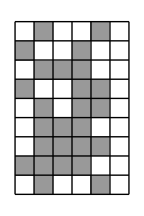

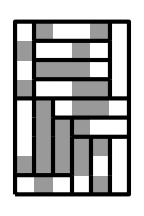

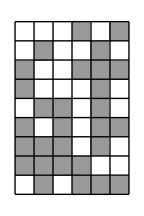

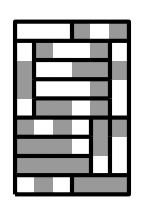

300

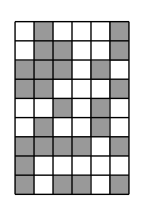

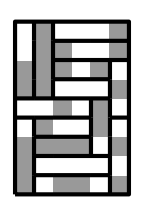

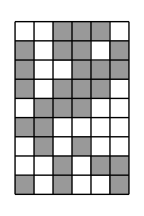

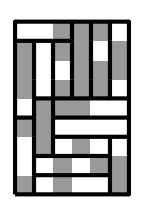

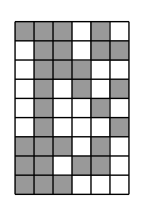

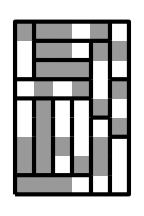

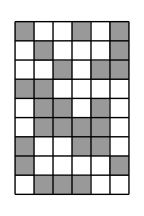

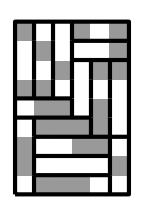

400

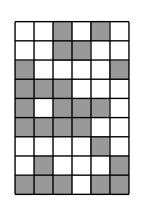

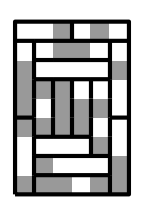

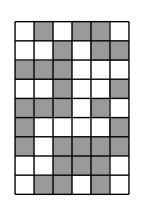

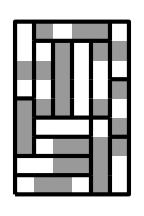

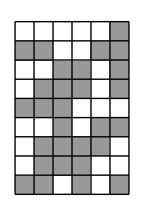

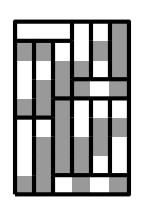

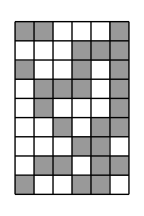

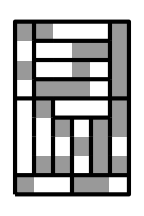

500

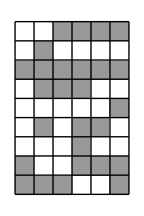

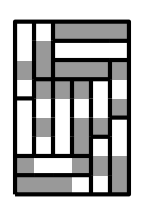

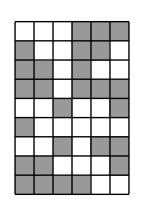

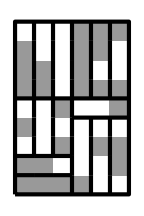

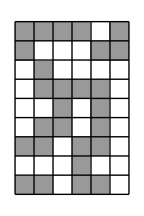

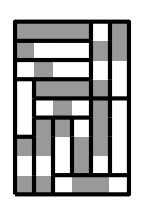

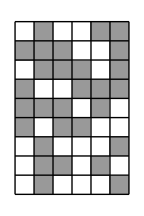

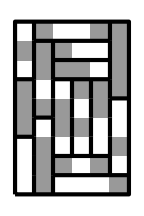

600

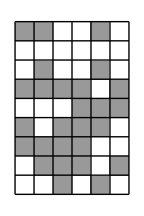

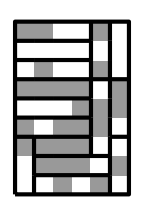

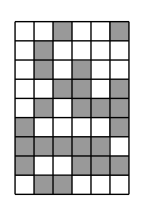

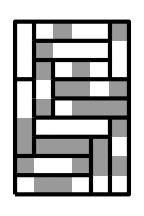

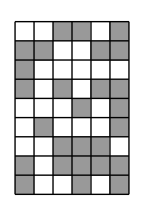

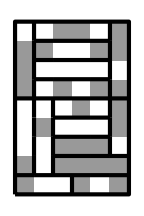

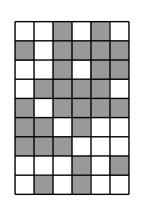

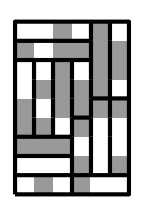

700

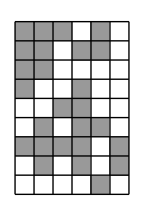

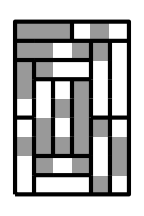

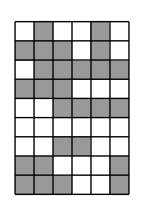

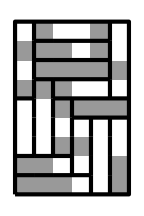

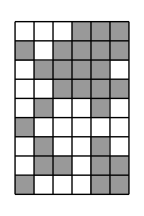

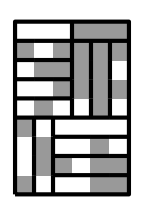

800

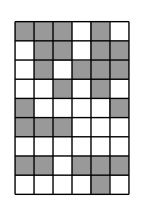

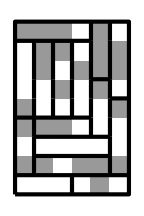

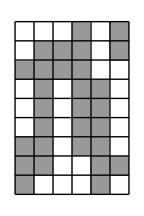

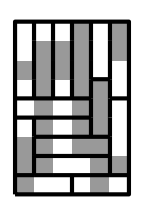

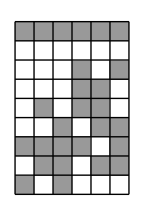

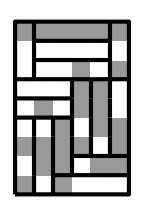

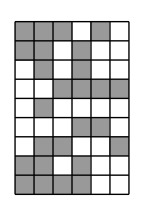

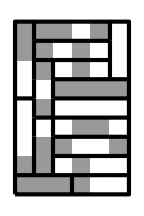

900

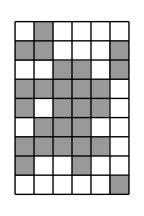

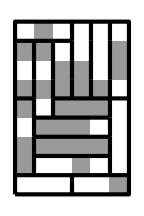

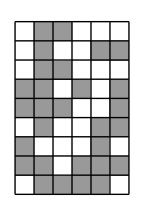

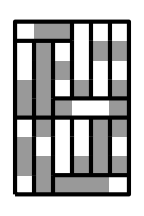

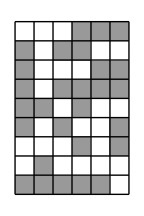

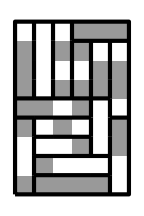

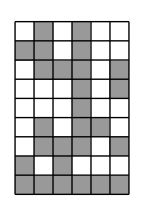

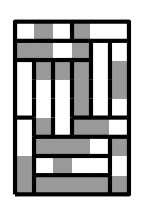

1000

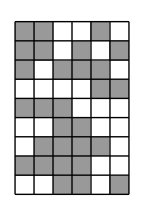

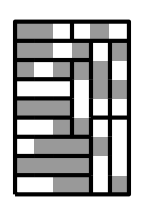

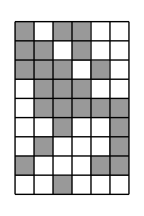

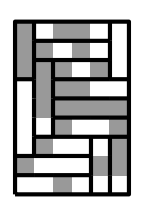

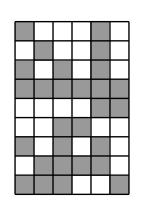

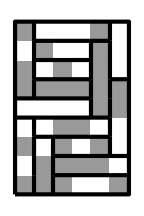

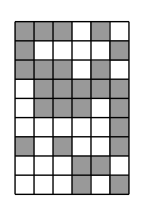

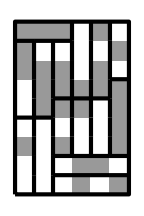

1100

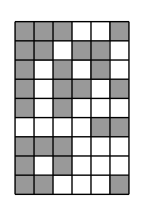

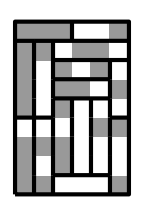

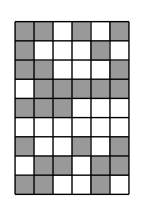

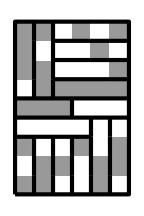

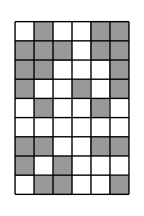

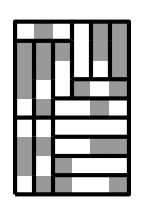

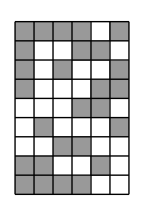

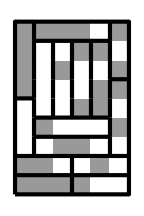

1200

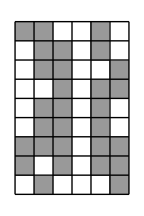

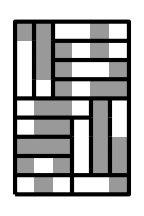

-Graphics-

-Graphics-

-Graphics-

«15 more identical outputs»

1300

-Graphics-

-Graphics-

-Graphics-

«11 more identical outputs»

1400

-Graphics-

-Graphics-

-Graphics-

«5 more identical outputs»

1500

-Graphics-

-Graphics-

-Graphics-

«11 more identical outputs»

1600

-Graphics-

-Graphics-

-Graphics-

«11 more identical outputs»

1700

-Graphics-

-Graphics-

-Graphics-

«17 more identical outputs»

1800

-Graphics-

-Graphics-

-Graphics-

«15 more identical outputs»

1900

-Graphics-

-Graphics-

-Graphics-

«5 more identical outputs»

2000

-Graphics-

-Graphics-

-Graphics-

«11 more identical outputs»

2100

-Graphics-

-Graphics-

-Graphics-

«11 more identical outputs»

2200

-Graphics-

-Graphics-

-Graphics-

«15 more identical outputs»

2300

-Graphics-

-Graphics-

-Graphics-

«13 more identical outputs»

2400

-Graphics-

-Graphics-

-Graphics-

«11 more identical outputs»

2500

-Graphics-

-Graphics-

-Graphics-

«19 more identical outputs»

2600

-Graphics-

-Graphics-

-Graphics-

«15 more identical outputs»

2700

-Graphics-

-Graphics-

-Graphics-

«19 more identical outputs»

2800

-Graphics-

-Graphics-

-Graphics-

«13 more identical outputs»

2900

-Graphics-

-Graphics-

-Graphics-

«19 more identical outputs»

3000

-Graphics-

-Graphics-

-Graphics-

«11 more identical outputs»

3100

-Graphics-

-Graphics-

-Graphics-

«11 more identical outputs»

3200

-Graphics-

-Graphics-

-Graphics-

«15 more identical outputs»

3300

-Graphics-

-Graphics-

-Graphics-

«19 more identical outputs»

3400

-Graphics-

-Graphics-

-Graphics-

«15 more identical outputs»

3500

-Graphics-

-Graphics-

-Graphics-

«13 more identical outputs»

3600

-Graphics-

-Graphics-

-Graphics-

«15 more identical outputs»

3700

-Graphics-

-Graphics-

-Graphics-

«19 more identical outputs»

3800

-Graphics-

-Graphics-

-Graphics-

«17 more identical outputs»

3900

-Graphics-

-Graphics-

-Graphics-

«9 more identical outputs»

4000

-Graphics-

-Graphics-

-Graphics-

«15 more identical outputs»

4100

-Graphics-

-Graphics-

-Graphics-

«17 more identical outputs»

4200

-Graphics-

-Graphics-

-Graphics-

«7 more identical outputs»

4300

-Graphics-

-Graphics-

-Graphics-

«5 more identical outputs»

4400

-Graphics-

-Graphics-

-Graphics-

«5 more identical outputs»

4500

-Graphics-

-Graphics-

-Graphics-

«11 more identical outputs»

4600

-Graphics-

-Graphics-

-Graphics-

«11 more identical outputs»

4700

-Graphics-

-Graphics-

-Graphics-

«17 more identical outputs»

4800

-Graphics-

-Graphics-

-Graphics-

«17 more identical outputs»

4900

-Graphics-

-Graphics-

-Graphics-

«7 more identical outputs»

5000

-Graphics-

-Graphics-

-Graphics-

«13 more identical outputs»

5100

-Graphics-

-Graphics-

-Graphics-

«15 more identical outputs»

5200

-Graphics-

-Graphics-

-Graphics-

«17 more identical outputs»

5300

-Graphics-

-Graphics-

-Graphics-

«11 more identical outputs»

5400

-Graphics-

-Graphics-

-Graphics-

«11 more identical outputs»

5500

-Graphics-

-Graphics-

-Graphics-

«15 more identical outputs»

5600

-Graphics-

-Graphics-

-Graphics-

«25 more identical outputs»

5700

-Graphics-

-Graphics-

-Graphics-

«9 more identical outputs»

5800

-Graphics-

-Graphics-

-Graphics-

«19 more identical outputs»

5900

-Graphics-

-Graphics-

-Graphics-

«5 more identical outputs»

6000

-Graphics-

-Graphics-

-Graphics-

«5 more identical outputs»

6100

-Graphics-

-Graphics-

-Graphics-

«7 more identical outputs»

6200

-Graphics-

-Graphics-

-Graphics-

«5 more identical outputs»

6300

-Graphics-

-Graphics-

-Graphics-

«13 more identical outputs»

6400

-Graphics-

-Graphics-

-Graphics-

«13 more identical outputs»

6500

-Graphics-

-Graphics-

-Graphics-

«11 more identical outputs»

6600

-Graphics-

-Graphics-

-Graphics-

«13 more identical outputs»

6700

-Graphics-

-Graphics-

-Graphics-

«17 more identical outputs»

6800

-Graphics-

-Graphics-

-Graphics-

«9 more identical outputs»

6900

-Graphics-

-Graphics-

-Graphics-

«25 more identical outputs»

7000

-Graphics-

-Graphics-

-Graphics-

«11 more identical outputs»

7100

-Graphics-

-Graphics-

-Graphics-

«9 more identical outputs»

7200

-Graphics-

-Graphics-

-Graphics-

«9 more identical outputs»

7300

-Graphics-

-Graphics-

-Graphics-

«11 more identical outputs»

7400

-Graphics-

-Graphics-

-Graphics-

«15 more identical outputs»

7500

-Graphics-

-Graphics-

-Graphics-

«19 more identical outputs»

7600

-Graphics-

-Graphics-

-Graphics-

«9 more identical outputs»

7700

-Graphics-

-Graphics-

-Graphics-

«25 more identical outputs»

7800

-Graphics-

-Graphics-

-Graphics-

«7 more identical outputs»

7900

-Graphics-

-Graphics-

-Graphics-

«11 more identical outputs»

8000

$Aborted